# ARITMÈTICA. PRÀCTICA 1. NOMBRES PRIMERS

### 1. Estudieu les funcions següents del Mathematica: FactorInteger, Divisors, Prime, PrimePi, PrimeQ:

```mathematica
?FactorInteger
```

FactorInteger[n] gives a list of the prime factors of the integer n, together with their exponents. 
FactorInteger[n,k] does partial factorization, pulling out at most k distinct factors.

Podem trobar dos casos:
- CAS 1: Introduïm com a input un nombre enter “n”. La funció retorna una llista de parells on el primer element és un  factor primers de n i el segon l’exponent del primer.

```mathematica
FactorInteger[124]
```

{{2,2},{31,1}}

- CAS 2: Introduïm com a input el nombre que volem factoritzar i el nombre màxim de factors que  volem. La funció retorna tants factors com hem demanat junt amb els seus exponents.(No tenen per què ser primers)

```mathematica
FactorInteger[124, 1]
```

{{124,1}}

```mathematica
?Divisors
```

Divisors[n] gives a list of the integers that divide n.

Input: nombre enter  n del que volem obtenir els divisors.
Output : llista dels enters que divideixen n.

```mathematica
Divisors[124]
```

```mathematica
{1,2,4,31,62,124}
```

```mathematica
?Prime
```

Prime[n] gives the n^th prime number.

Input : posició del nombre primer que volem obtenir.
Output: enèssim nombre primer.

```mathematica
Prime[5]
```

11

```mathematica
?PrimePi
```

PrimePi[x] gives the number of primes π(x) less than or equal to x.

Input: cota superior
Output: nombre de primers que es troben per sota o són iguals a la cota superior.

```mathematica
PrimePi[124]
```

```mathematica
30
```

```mathematica
?PrimeQ
```

PrimeQ[expr] yields True if expr is a prime number, and yields False otherwise.

Input: expressió matemàtica
Output: boolean, true or false depenent si l’expressió és un nombre primer(True) o compost(False).

```mathematica
PrimeQ[5]
```

True

## 2. Utilitza la comanda Table[expre, {i, max}] per escriure la taula dels 1000 primers nombres primers:

```mathematica
?Table
```

Table[expr,n] generates a list of n copies of expr. 
Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
Table[expr,{i,i_min,i_max}] starts with i=i_min. 
Table[expr,{i,i_min,i_max,di}] uses steps di. 
Table[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Table[expr,{i,i_min,i_max},{j,j_min,j_max},…] gives a nested list. The list associated with i is outermost.

RECORDA!  Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
P.t. sempre comença per l’1 i acaba en el max establert. La variable de l’expressió ha de coincidir amb la variable del primer valor.

```mathematica
Table[Prime[i], {i, 1000}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541,547,557,563,569,571,577,587,593,599,601,607,613,617,619,631,641,643,647,653,659,661,673,677,683,691,701,709,719,727,733,739,743,751,757,761,769,773,787,797,809,811,821,823,827,829,839,853,857,859,863,877,881,883,887,907,911,919,929,937,941,947,953,967,971,977,983,991,997,1009,1013,1019,1021,1031,1033,1039,1049,1051,1061,1063,1069,1087,1091,1093,1097,1103,1109,1117,1123,1129,1151,1153,1163,1171,1181,1187,1193,1201,1213,1217,1223,1229,1231,1237,1249,1259,1277,1279,1283,1289,1291,1297,1301,1303,1307,1319,1321,1327,1361,1367,1373,1381,1399,1409,1423,1427,1429,1433,1439,1447,1451,1453,1459,1471,1481,1483,1487,1489,1493,1499,1511,1523,1531,1543,1549,1553,1559,1567,1571,1579,1583,1597,1601,1607,1609,1613,1619,1621,1627,1637,1657,1663,1667,1669,1693,1697,1699,1709,1721,1723,1733,1741,1747,1753,1759,1777,1783,1787,1789,1801,1811,1823,1831,1847,1861,1867,1871,1873,1877,1879,1889,1901,1907,1913,1931,1933,1949,1951,1973,1979,1987,1993,1997,1999,2003,2011,2017,2027,2029,2039,2053,2063,2069,2081,2083,2087,2089,2099,2111,2113,2129,2131,2137,2141,2143,2153,2161,2179,2203,2207,2213,2221,2237,2239,2243,2251,2267,2269,2273,2281,2287,2293,2297,2309,2311,2333,2339,2341,2347,2351,2357,2371,2377,2381,2383,2389,2393,2399,2411,2417,2423,2437,2441,2447,2459,2467,2473,2477,2503,2521,2531,2539,2543,2549,2551,2557,2579,2591,2593,2609,2617,2621,2633,2647,2657,2659,2663,2671,2677,2683,2687,2689,2693,2699,2707,2711,2713,2719,2729,2731,2741,2749,2753,2767,2777,2789,2791,2797,2801,2803,2819,2833,2837,2843,2851,2857,2861,2879,2887,2897,2903,2909,2917,2927,2939,2953,2957,2963,2969,2971,2999,3001,3011,3019,3023,3037,3041,3049,3061,3067,3079,3083,3089,3109,3119,3121,3137,3163,3167,3169,3181,3187,3191,3203,3209,3217,3221,3229,3251,3253,3257,3259,3271,3299,3301,3307,3313,3319,3323,3329,3331,3343,3347,3359,3361,3371,3373,3389,3391,3407,3413,3433,3449,3457,3461,3463,3467,3469,3491,3499,3511,3517,3527,3529,3533,3539,3541,3547,3557,3559,3571,3581,3583,3593,3607,3613,3617,3623,3631,3637,3643,3659,3671,3673,3677,3691,3697,3701,3709,3719,3727,3733,3739,3761,3767,3769,3779,3793,3797,3803,3821,3823,3833,3847,3851,3853,3863,3877,3881,3889,3907,3911,3917,3919,3923,3929,3931,3943,3947,3967,3989,4001,4003,4007,4013,4019,4021,4027,4049,4051,4057,4073,4079,4091,4093,4099,4111,4127,4129,4133,4139,4153,4157,4159,4177,4201,4211,4217,4219,4229,4231,4241,4243,4253,4259,4261,4271,4273,4283,4289,4297,4327,4337,4339,4349,4357,4363,4373,4391,4397,4409,4421,4423,4441,4447,4451,4457,4463,4481,4483,4493,4507,4513,4517,4519,4523,4547,4549,4561,4567,4583,4591,4597,4603,4621,4637,4639,4643,4649,4651,4657,4663,4673,4679,4691,4703,4721,4723,4729,4733,4751,4759,4783,4787,4789,4793,4799,4801,4813,4817,4831,4861,4871,4877,4889,4903,4909,4919,4931,4933,4937,4943,4951,4957,4967,4969,4973,4987,4993,4999,5003,5009,5011,5021,5023,5039,5051,5059,5077,5081,5087,5099,5101,5107,5113,5119,5147,5153,5167,5171,5179,5189,5197,5209,5227,5231,5233,5237,5261,5273,5279,5281,5297,5303,5309,5323,5333,5347,5351,5381,5387,5393,5399,5407,5413,5417,5419,5431,5437,5441,5443,5449,5471,5477,5479,5483,5501,5503,5507,5519,5521,5527,5531,5557,5563,5569,5573,5581,5591,5623,5639,5641,5647,5651,5653,5657,5659,5669,5683,5689,5693,5701,5711,5717,5737,5741,5743,5749,5779,5783,5791,5801,5807,5813,5821,5827,5839,5843,5849,5851,5857,5861,5867,5869,5879,5881,5897,5903,5923,5927,5939,5953,5981,5987,6007,6011,6029,6037,6043,6047,6053,6067,6073,6079,6089,6091,6101,6113,6121,6131,6133,6143,6151,6163,6173,6197,6199,6203,6211,6217,6221,6229,6247,6257,6263,6269,6271,6277,6287,6299,6301,6311,6317,6323,6329,6337,6343,6353,6359,6361,6367,6373,6379,6389,6397,6421,6427,6449,6451,6469,6473,6481,6491,6521,6529,6547,6551,6553,6563,6569,6571,6577,6581,6599,6607,6619,6637,6653,6659,6661,6673,6679,6689,6691,6701,6703,6709,6719,6733,6737,6761,6763,6779,6781,6791,6793,6803,6823,6827,6829,6833,6841,6857,6863,6869,6871,6883,6899,6907,6911,6917,6947,6949,6959,6961,6967,6971,6977,6983,6991,6997,7001,7013,7019,7027,7039,7043,7057,7069,7079,7103,7109,7121,7127,7129,7151,7159,7177,7187,7193,7207,7211,7213,7219,7229,7237,7243,7247,7253,7283,7297,7307,7309,7321,7331,7333,7349,7351,7369,7393,7411,7417,7433,7451,7457,7459,7477,7481,7487,7489,7499,7507,7517,7523,7529,7537,7541,7547,7549,7559,7561,7573,7577,7583,7589,7591,7603,7607,7621,7639,7643,7649,7669,7673,7681,7687,7691,7699,7703,7717,7723,7727,7741,7753,7757,7759,7789,7793,7817,7823,7829,7841,7853,7867,7873,7877,7879,7883,7901,7907,7919}

#### 3. És cert que tots els nombres de la forma n^2 - n + 41, n pertanyent als N, són primers?

Fals, per tal de demostrar-ho mirarem si els 100 primers nombres de l’expressió són primers aplicant la funció PrimeQ[n]. Si algun d’aquests nombres retorna False, aleshores ja haurem trobat el nostre contraexemple que refuta l’enunciat. En cas contrari, evaluarem els 100 nombres seguents fins que la funció ens retorni False. 
 ho demostrem amb un contraexemple.

```mathematica
Table[PrimeQ[n^2-n +41], {n, 100}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,True,True,False,True,True,True,True,False,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,False,False,True,False,True,True,False,True,False,True,False,True,True,True,True,False,True,True,True}

Sigui n = 41,

```mathematica
PrimeQ[(41^2 )-41 + 41]
```

False

```mathematica
P.t. queda refutat l'enunciat.
```

## 4. Defineix una funció Fermat que calculi els nombres de Fermat :=( 2^2^n) +1. Escriu una taula amb els 10 primers nombres de Fermat. Digues quins d’ells són primers:

```mathematica
Fermat[n_]:= 2^(2^n)+1
```

```mathematica
t =Table[{n,PrimeQ[Fermat[n]],Fermat[n]},{n,1,10}]
```

{{1,True,5},{2,True,17},{3,True,257},{4,True,65537},{5,False,4294967297},{6,False,18446744073709551617},{7,False,340282366920938463463374607431768211457},{8,False,115792089237316195423570985008687907853269984665640564039457584007913129639937},{9,False,13407807929942597099574024998205846127479365820592393377723561443721764030073546976801874298166903427690031858186486050853753882811946569946433649006084097},{10,False,179769313486231590772930519078902473361797697894230657273430081157732675805500963132708477322407536021120113879871393357658789768814416622492847430639474124377767893424865485276302219601246094119453082952085005768838150682342462881473913110540827237163350510684586298239947245938479716304835356329624224137217}}

Taula de la forma: {número evaluat, és primer el nombre de fermat?,  nombre de fermat}

### 5. És primer el nombre 10^10 +1? Detemina un nombre primer que tingui més de 10 xifres decimals. Quin és el primer més petit que té més de 10 xifres decimals?

```mathematica
PrimeQ[10^10 + 1]
```

False

Per tant, queda provat que n = 10^10 +1 no és un nombre primer.

Ho tornarem a demostrar de la mateixa manera que en l’exercici anterior. Comprovem amb la funció PrimeQ si algun dels 100 primers nombres de la forma (10^10 + n) amb n ∈ {1, 100} són primers. En cas afirmatiu ens aturem perquè ja hem trobat el que demana l’enunciat. De no ser això, evaluem els 100 següents nombres, i∈ {101, 200} fins a que la funció retorni en algun moment True.

```mathematica
t =Table[{10^10+n,PrimeQ[10^10+n]}, {n, 100}]
```

{{10000000001,False},{10000000002,False},{10000000003,False},{10000000004,False},{10000000005,False},{10000000006,False},{10000000007,False},{10000000008,False},{10000000009,False},{10000000010,False},{10000000011,False},{10000000012,False},{10000000013,False},{10000000014,False},{10000000015,False},{10000000016,False},{10000000017,False},{10000000018,False},{10000000019,True},{10000000020,False},{10000000021,False},{10000000022,False},{10000000023,False},{10000000024,False},{10000000025,False},{10000000026,False},{10000000027,False},{10000000028,False},{10000000029,False},{10000000030,False},{10000000031,False},{10000000032,False},{10000000033,True},{10000000034,False},{10000000035,False},{10000000036,False},{10000000037,False},{10000000038,False},{10000000039,False},{10000000040,False},{10000000041,False},{10000000042,False},{10000000043,False},{10000000044,False},{10000000045,False},{10000000046,False},{10000000047,False},{10000000048,False},{10000000049,False},{10000000050,False},{10000000051,False},{10000000052,False},{10000000053,False},{10000000054,False},{10000000055,False},{10000000056,False},{10000000057,False},{10000000058,False},{10000000059,False},{10000000060,False},{10000000061,True},{10000000062,False},{10000000063,False},{10000000064,False},{10000000065,False},{10000000066,False},{10000000067,False},{10000000068,False},{10000000069,True},{10000000070,False},{10000000071,False},{10000000072,False},{10000000073,False},{10000000074,False},{10000000075,False},{10000000076,False},{10000000077,False},{10000000078,False},{10000000079,False},{10000000080,False},{10000000081,False},{10000000082,False},{10000000083,False},{10000000084,False},{10000000085,False},{10000000086,False},{10000000087,False},{10000000088,False},{10000000089,False},{10000000090,False},{10000000091,False},{10000000092,False},{10000000093,False},{10000000094,False},{10000000095,False},{10000000096,False},{10000000097,True},{10000000098,False},{10000000099,False},{10000000100,False}}

Table::iterb: Iterator {n, 10000000000, 10000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000} does not have appropriate bounds.

```mathematica
□paclet:ref/Off
```

Table::iterb: Iterator {n,10000000000,10000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000} does not have appropriate bounds.

Table::itraw: Raw object 1 cannot be used as an iterator.

### 6. Escriu la funció següent:

```mathematica
PrimerSegüent[n_]:= Module[{k=n}, 
While[!PrimeQ[k], k++];
k]
```

```mathematica
PrimerSegüent[6]
```

7

```mathematica
?Module
```

Module[{x,y,…},expr] specifies that occurrences of the symbols x, y, … in expr should be treated as local. 
Module[{x=x_0,…},expr] defines initial values for x, ….

Module transforma la variable global n ∈ Z en una variable local k per a poder operar amb ella dins la funció.
PrimeQ evalua la variable. Mentres que k no sigui primer, augmentem una unitat k , si k és primer, imprimim k i ens aturem.
Utilitat: trobar el nombre primer correlativament superior o igual al nombre introduït.

```mathematica
PrimerSegüent[10^10+1]
```

10000000019

### 7. Defineix la funció PrimerAnterior[n_]

```mathematica
PrimerAnterior[n_]:= Module[{k= n},
While[!PrimeQ[k], k--];
k]
```

```mathematica
PrimerAnterior[10^10]
```

```mathematica
9999999967
```

### 8. Considera la funció TNP[x_]:= N[PrimePi[x]/(x/Log[x])]. Escriu una taula amb els valors PrimePi[10^n], N[10^n/Log[10^n]], TNP[10^n], per a 1<= n<= 13. Observa el comportament de les entrades.

```mathematica
t1 = Table[{n,PrimePi[10^n]}, {n, 1, 13}]
```

{{1,4},{2,25},{3,168},{4,1229},{5,9592},{6,78498},{7,664579},{8,5761455},{9,50847534},{10,455052511},{11,4118054813},{12,37607912018},{13,346065536839}}

En la funció t1 observem que a mesura que n va augmentant, el ratio de creixement de nombres primers disminueix dràsticament.

```mathematica
Plot[PrimePi[n]/10^n, {n, 1, 13}]
```

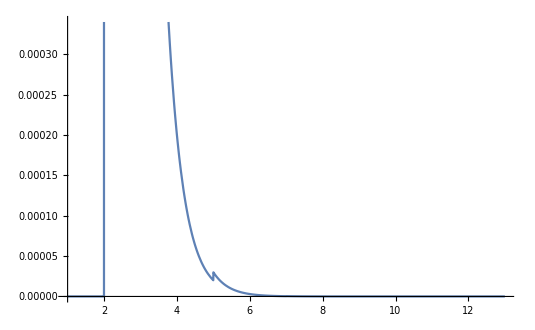

```mathematica
t2 = Table[{n,N[10^n / Log[10^n]]}, {n, 1, 13}]
```

{{1,4.34294},{2,21.7147},{3,144.765},{4,1085.74},{5,8685.89},{6,72382.4},{7,620421.},{8,5.42868×10^6},{9,4.82549×10^7},{10,4.34294×10^8},{11,3.94813×10^9},{12,3.61912×10^10},{13,3.34073×10^11}}

```mathematica
TableForm[t2]
```

```mathematica
{{1, 4.3429448190325175}, {2, 21.714724095162588}, {3, 144.76482730108395}, {4, 1085.7362047581294}, {5, 8685.889638065037}, {6, 72382.41365054197}, {7, 620420.6884332169}, {8, 5.428681023790647*^6}, {9, 4.825494243369465*^7}, {10, 4.342944819032518*^8}, {11, 3.9481316536659255*^9}, {12, 3.619120682527099*^10}, {13, 3.340726783871168*^11}}
```

Simplement observem que els valors de l’output augmenten a mesura que n augmenta, tendint cap a l’infinit.

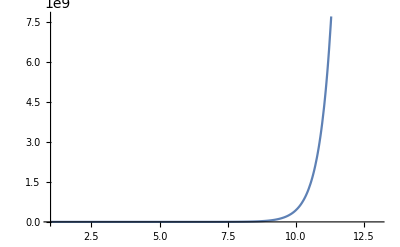

```mathematica
Plot[N[10^n / Log[10^n]], {n, 1, 13}]
```

```mathematica
TNP[x_]:=N[PrimePi[x]/(x/Log[x])]
t3 = Table[{n,TNP[10^n]}, {n, 1, 13}]
```

```mathematica
{{1,0.9210340371976184},{2,1.151292546497023},{3,1.160502886868999},{4,1.1319508317158729},{5,1.1043198105999443},{6,1.0844899477790795},{7,1.071174788961823},{8,1.0612992317564809},{9,1.053726964235171},{10,1.047797128358109},{11,1.0430388787000802},{12,1.0391450110953409},{13,1.0358989502218021}}
```

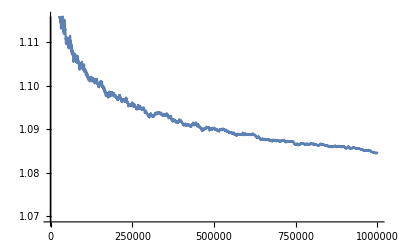

```mathematica
Plot[N[PrimePi[n]/(n/Log[n])], {n,1,1000000}]
```

Podem observar que el numerador és la primera funció i el denominador la segona. Per tant, el numerador cada cop anirà augmentant més lentament mentre que el denominador tendirà  cap a l’infinit. La funció en un inici creixerà ja que el numerador serà major, però per n molt grans, la funció tendirà cap al 1 ja que π(x) ≈ x /log(x)

### 9. Cerca referència sobre el teorema dels nombres primers

Extet del llibre “Elementary number therory and its applications”.
Teorema dels nombres primers.  Sigui π(x) la funció que denota la quantitat de nombres primers que no excedeixen a x, el teorema estableix que el quocient de π(x) per x/ln(x) s’apropa a 1 a mesura que x creix snese cap cota superior que el limiti. En el llenguatge dels límits, tenim que el límit quan x tendeix a ∞ de l’expressió π(x)/ x/ln(x) és igual a 1. Ho podem veure demostrat en l’exercici anterior.

Power::infy: Infinite expression 1/0 encountered.